This notebook takes a list of parameters & their negative log likelihoods, and interpolates to give a smooth sampling.  It then uses the Metropolis algorithm to sample parameter sets in proportion to their likelihood.

SetDirectory to point to the data file, and Evaluate Initialisation

#### The data

The data are supplied as a list of the form {N_0,r,K,M,T,-log(L)}

```mathematica
data[[1]]
```

{20,0.025,250,0,1.33333,7018.16}

These are the parameter values supplied:

```mathematica
Union/@Drop[Transpose[data],-1]
```

{{20,40,80,160,320},{0.025,0.05,0.1,0.2,0.4},{250,500,1000,2000,4000},{0,1,2,4,8},{1.33333,1.66667,2}}

### Interpolation on a log scale

The parameter grid is evenly spaced on a log scale, and so the interpolation is also on a log scale. (Interpolating on the original scale causes problems, because the parameters are then unevenly spaced).  The interpolation passes through every data point, and fills in-between using a cubic curve.   Because M=0 is included, the transformation is lM=log[M+0.5], M=Exp[lM]-0.5

Note: this uses natural logs

This transforms to a (natural) log scale, and interpolates.  The error message arises because there are only three generation times, and so thhe interpolation uses a quadratic rather than a cubic.

```mathematica
intB=Interpolation[data/.{n_,r_,k_,M_,t_,L_}:>{Log[n],Log[r],Log[k],Log[M+0.5],t,L}]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,3,3,3,2}.

InterpolatingFunction[…]

This fixes M=4, T=2 and finds the MLE for {log[N_0],log[r],log[K]}, starting the search somewhere plausible {80, 0.1, K=800}, and setting bounds on the search domain:

```mathematica
fmb=FindMinimum[intB[ln,lr,lk,Log[4+0.5],2],{ln,Log[80],Log[20],Log[320]},{lr,Log[0.1],Log[0.025],Log[0.4]},{lk,Log[800],Log[250],Log[4000]}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{5666.39,{ln→4.08265,lr→-2.12234,lk→7.23995}}

This also allows M to vary, which slightly increases the likelihood:

```mathematica
fmb1=FindMinimum[intB[ln,lr,lk,lm,2],{ln,Log[80],Log[20],Log[320]},{lr,Log[0.1],Log[0.025],Log[0.4]},{lk,Log[800],Log[250],Log[4000]},{lm,Log[4+0.5],Log[0.5],Log[8+0.5]}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{5662.62,{ln→3.9973,lr→-2.0709,lk→7.19375,lm→1.32586}}

These are the MLE on the original scale, allowing M to vary, or fixing it at 4:

```mathematica
Exp[{ln,lr,lk,lm}/.fmb1[[2]]]+{0,0,0,0.5}
```

{54.4509,0.126072,1331.09,4.26541}

```mathematica
Exp[{ln,lr,lk}/.fmb[[2]]]
```

{59.3027,0.119751,1394.02}

The minimum in the data is only slightly higher than the MLE, which seems reasonable:

```mathematica
intB[Log[80],Log[0.1],Log[2000],Log[4+0.5],2]
```

5669.36

The left plot fixes T=2, M=3.26, r=0.1202, the right plot fixes N_0=55.6, K=1335.  Contours are spaced at unit intervals. For 2 degrees of freedom, a loss of log(L) of 3 corresponds to χ_2^2=6, or P=5%; thus, three contours down give the 3-unit support limits, corresponding to 95% confidence intervals.

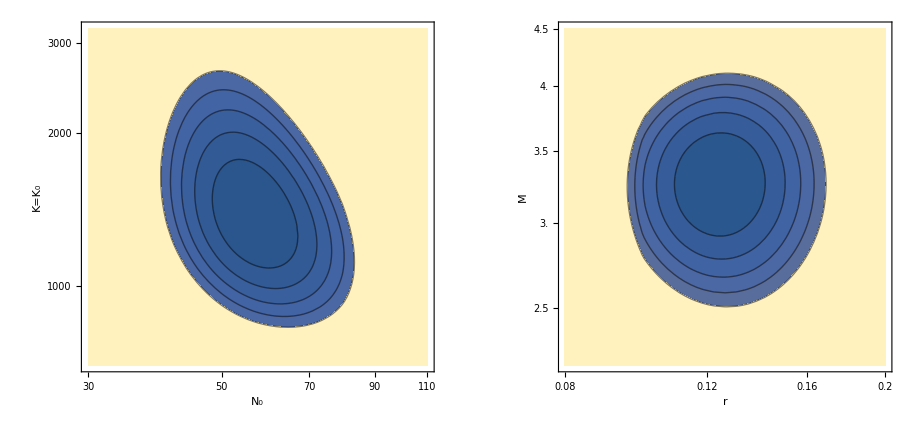

```mathematica
frt[x_]:={Log[x],ToString[x]};
frtm[x_]:={Log[x+0.5],ToString[x]};
mn=(Min[Last/@xl]);GraphicsRow[{ContourPlot[intB[ln,Log[0.1202],lk,Log[3.265+0.5],2]-mn,{ln,Log[30],Log[110]},{lk,Log[700],Log[3200]},Contours->Range[0,5],FrameLabel->{"N_0","K=K_0"},FrameTicks->{frt/@Range[30,110,20],frt/@Range[1000,3000,1000]}],
ContourPlot[intB[Log[55.6],lr,Log[1335],lm,2]-mn,{lr,Log[0.08],Log[0.2]},{lm,Log[2.2+0.5],Log[4.5+0.5]},Contours->Range[0,5],FrameTicks->{frt/@Range[0.08,0.2,0.02],frtm/@Range[2,4.5,0.5]},FrameLabel->{"r","M"}]}]
```

#### Optimising N_0, r for given K

If we optimise N_0 and r for given K, we get a smooth function with a definite minimum

```mathematica
fmtb=Table[Prepend[FindMinimum[intB[ln,lr,lk,Log[4+0.5],2],{ln,Log[60],Log[20],Log[320]},{lr,Log[0.12],Log[0.025],Log[0.4]}],Exp[lk]],{lk,Log[250.],Log[4000],Log[4000/250]/10}];
TableForm[fmtb,TableDepth->2]
```

250. | 5757.92 | {ln→5.26271,lr→-0.916291}
329.877 | 5722.78 | {ln→4.2954,lr→-1.75283}
435.275 | 5699.43 | {ln→4.12883,lr→-1.76095}
574.349 | 5683.25 | {ln→4.04163,lr→-1.80412}
757.858 | 5673.21 | {ln→4.00897,lr→-1.875}
1000. | 5668.08 | {ln→4.01932,lr→-1.97126}
1319.51 | 5666.43 | {ln→4.07061,lr→-2.09685}
1741.1 | 5666.89 | {ln→4.13516,lr→-2.22506}
2297.4 | 5668.36 | {ln→4.15695,lr→-2.30259}
3031.43 | 5670.36 | {ln→4.10421,lr→-2.30259}
4000. | 5672.12 | {ln→4.05919,lr→-2.30259}

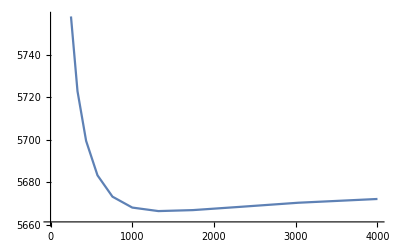

```mathematica
ListLinePlot[fmtb/.{k_,l_,rl_List}:>{k,l}]
```

#### MLE for three values of T

Note: this uses natural logs

These are -log(L) and the MLE for the three values of  T. T=2 seems most likely; the choice of T makes little difference to the estimates.

```mathematica
TableForm[Prepend[{tvalues[[#]],fm[#][[1]],Exp[ln],Exp[lr],Exp[lk],Exp[lm]-0.5}/.fm[#][[2]]&/@{1,2,3},
{"T","-log(L)","N_0","r","K","M"}]]
```

T | -log(L) | N_0 | r | K | M
1.33333 | 5665.23 | 55.4199 | 0.102179 | 4000. | 3.23059
1.66667 | 5663.39 | 55.5942 | 0.120153 | 1335.05 | 3.26502
2 | 5662.62 | 54.4509 | 0.126072 | 1331.09 | 3.26541

#### Generating 5×10^5 random values, for T=2; burn-in of 10^4

```mathematica
burn=10^4;run=5 10^5;
Timing[xl=Drop[randomWalk[burn+run,1.05,3],burn];]
```

{483.009,Null}

The file contains 5 10^5 values of {N_0,r,K,M,-log(L)}:

```mathematica
Export["random values 23 Sept 2023.csv",Flatten/@xl];
```

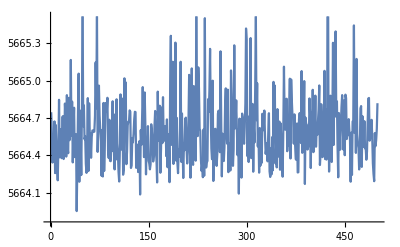

```mathematica
ListLinePlot[Mean/@Partition[Last/@xl,1000]]
```

#### Distribution of the parameters (T=2)

Posterior distribution (points) superimposed on contours of log likelihood (spacing 1).  Left: N_0 vs K. right: r vs.M .  Contours on the left plot fixes T=2, M=3.26, r=0.1202;  the right plot fixes N_0=55.6, K=1335.  Note that these distributions are not quite the same: the posterior distribution averages over the posterior distribution of the other two parameters, whereas the contours show the log likelihood with the other two parameters fixed at their MLE.

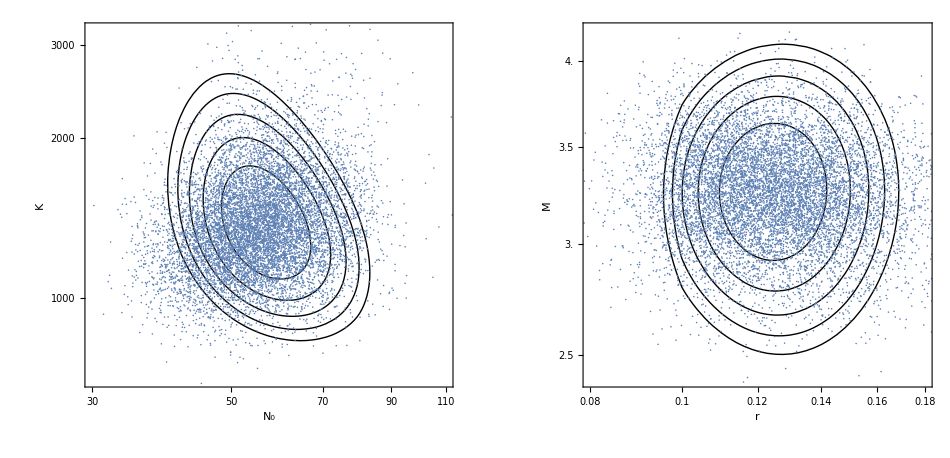

```mathematica
mn=(Min[Last/@xl]);
frt[x_]:={Log[x],ToString[x]};
frtm[x_]:={Log[x+0.5],ToString[x]};
GraphicsRow[{Show[ContourPlot[intB[ln,Log[0.1202],lk,Log[3.765],2]-mn,{ln,Log[30],Log[110]},{lk,Log[700],Log[3200]},Contours->Range[-1,5],FrameLabel->{"N_0","K"},FrameTicks->{frt/@Range[30,110,20],frt/@Range[1000,3000,1000]},ContourShading->None],ListPlot[xl[[1;;-1;;50,1,{1,3}]],AxesLabel->{"N_0","K"},AspectRatio->1]],
Show[ContourPlot[intC[2][Log[55.59],lr,Log[1335],lm]-mn,{lr,Log[0.07],Log[0.2]},{lm,Log[2+0.5],Log[4.5+0.5]},Contours->Range[-1,5],FrameTicks->{frt/@Range[0.08,0.18,0.02],frtm/@Range[2.5,4.2,0.5]},FrameLabel->{"r","M"},ContourShading->None,PlotRange->{{Log[0.08],Log[0.18]},{Log[2.4+0.5],Log[4.2+0.5]}}],ListPlot[Transpose[{xl[[1;;-1;;50,1,2]],xl[[1;;-1;;50,1,4]]}],AxesLabel->{"r","M"}],AspectRatio->1]}]
```

These are the posterior distributions of the 4 parameters, for T=2:

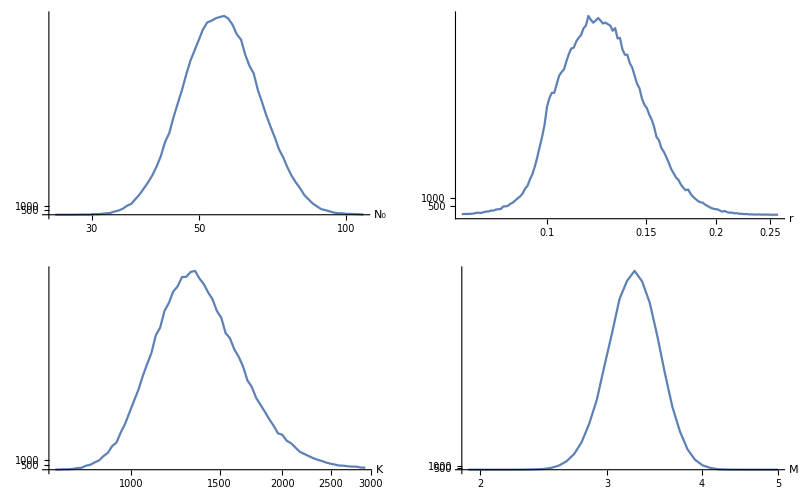

```mathematica
gr::usage="gr[j,δ,{x0,x1},ticks] plots the posterior distribution for parameter j, with bin size δ and specified ticks";
lab={"N_0","r","K","M"};
tl[tks_List,Δ_]:={Log[#+Δ],ToString[#]}&/@tks;
gr[j_Integer,δ_,{x0_,x1_},tks_List]:=Module[{Δ=If[j==4,0.5,0]},
ListLinePlot[Transpose[{Range[Log[x0+Δ]+δ/2,Log[x1+Δ]-δ/2,δ],BinCounts[xl[[All,1,j]],{Log[x0+Δ],Log[x1+Δ],δ}]}],AxesLabel->{lab[[j]],None},Ticks->{tl[tks,Δ],{500,1000}}]];
GraphicsGrid[
{{gr[1,0.02,{25,110},{30,50,100}],gr[2,0.01,{0.07,0.26},{0.1,0.15,0.2,0.25}]},
{gr[3,0.02,{700,3000},{1000,1500,2000,2500,3000}],gr[4,0.02,{1.9,5.1},{2,3,4,5}]}}]
```

These are the mean and the 95% limits of the posterior distribution:

```mathematica
TableForm[Prepend[Table[
(Δ=If[j==4,0.5,0];{lab[[j]],Exp[Mean[xl[[All,1,j]]]]-Δ,Exp[limits[xl[[All,1,j]],0.05]]-Δ}),{j,4}],{"","mean","95% limits"}],TableDepth->2]
```

| mean | 95% limits
N_0 | 55.3948 | {39.1577,79.1246}
r | 0.124778 | {0.0922092,0.175655}
K | 1370.91 | {949.594,2168.92}
M | 3.25047 | {2.76906,3.7712}

#### Some checks

The mean of the random walk (top) is close to the MLE (bottom)

```mathematica
mn=Mean[xl[[All,1]]];mle={ln,lr,lk,lm}/.fm[2][[2]];
TableForm[Join[{{"N_0","r","K","M"}},Append[Exp[#[[1;;3]]],Exp[#[[4]]]-0.5]&/@{mn,mle}]]
```

N_0 | r | K | M
55.3948 | 0.124778 | 1370.91 | 3.25047
55.5942 | 0.120153 | 1335.05 | 3.26502

The minimum -log(L) achieved in the random walk (top) is slightly better than the estimated MLE from interpolation.  -2log(L) should follow a χ_4^2 distribution. The mean -2log(L) in the random walk is 3.97 above this, about the same as the predicted 4 (the # of parameters), and the variance is also close to the predicted 8

```mathematica
ml=Min[xl[[All,-1]]];
TableForm[{{ml,2(Mean[xl[[All,-1]]]-ml),4Variance[xl[[All,-1]]]},
{fm[2][[1]],Mean[ChiSquareDistribution[4]],Variance[ChiSquareDistribution[4]]}}]
```

5662.62 | 3.97153 | 8.24493
5663.39 | 4 | 8

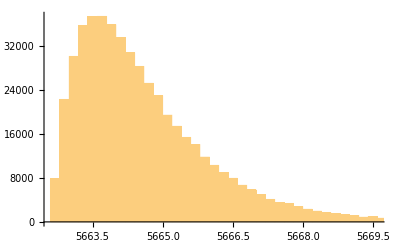

```mathematica
Histogram[xl[[All,-1]]]
```

There is no suggestion of a systematic change in -log(L) over the random walk. This plots the means of every 1000 points:

```mathematica
ListLinePlot[Mean/@Partition[xl[[All,-1]],1000]]
```

-Graphics-

## Definitions

```mathematica
SetDirectory["/Users/NickBarton/Manuscripts/Skerries/"];(* set this directory to point to the data file *)
data::usage="data stores an array where each row gives the 5 parameters, followed by the negative log likelihood, in the form {N0,r,K,M,T,-log(L)}";
data=Flatten[Map[StringSplit,Import["SEQSNPTM004_RESULTS Aug23.txt","CSV"],{2}],1];
data=Map[ToExpression,Drop[data,1],{2}];
```

```mathematica
tvalues::usage="tvalues lists the three values of t";
tvalues=Union[data[[All,5]]];
```

```mathematica
intC::usage="intC[t] stores an interpolation on log[N_0],log[r],log[K],log[M+0.5], given t (which must be one tvalues)";
intC[t_]:=intC[t]=
Interpolation[Cases[data,{_,_,_,_,t,_}]/.{n_,r_,k_,M_,_,L_}:>{Log[n],Log[r],Log[k],Log[0.5+M],L}];
```

```mathematica
intD::usage="intD[t] gives an interpolation on log[N_0],log[r],log[K],log[M+0.5], given t (which must be one tvalues). Returns ∞ if the arguments lie outside the range of the interpolation, as given by intC[t][[1]].";
intD[t_][x_List]:=If[withinQ[intC[t][[1]]][x],intC[t]@@x,∞];
```

```mathematica
withinQ::usage="withinQ[{{x_(1, 0),x_(1, 1)},…}][{x_1,…}] checks whether the point is within a rectabgular domain"; 
withinQ[xl_List][x_List]:=And@@MapThread[#2[[1]]≤#1≤#2[[2]]&,{x,xl}];
```

```mathematica
fm::usage="fm[j] gives minimises wrt log[N_0],log[r],log[K],log[M+0.5]; j=1,2,3 corresponds to t=1.333, 1.667, 2";
fm[j_]:=fm[j]=Module[{t=Union[data[[All,5]]][[j]]},
FindMinimum[intC[t][ln,lr,lk,lm],{ln,Log[100],Log[20],Log[320]},{lr,Log[0.1],Log[0.025],Log[0.4]},{lk,Log[2000],Log[250],Log[4000]},{lm,Log[4+0.5],Log[0+0.5],Log[8+0.5]}]];
```

```mathematica
randomWalk::usage="randomWalk[n,λ,j] makes n random draws from the posterior distribution; j=1,2,3 corresponds to the three values of T.  If a trial is rejected, the step is decreased by a factor λ, and vice versa.";
randomWalk[n_Integer,λ_,j:(1|2|3)]:=Module[{δ=0.1,x,L,xL,L1,dx,τ=tvalues[[j]]},
x=Mean/@intC[τ][[1]];L=intD[τ][x];xL={{x,L}};
Do[dx=δ RandomReal[{-1,1},4];
L1=intD[τ][x+dx];
If[Exp[L-L1]>Random[],
x=x+dx;δ=δ*λ;L=L1,
δ=δ/λ];
AppendTo[xL,{x,L}],{n}];
xL];
```

```mathematica
limits::usage="limits[{x_1,…},P] gives the parameter range that includes a fraction 1-P, with P/2 on each side.";
limits[x_List,p_]:=Module[{k=Round[Length[x](p/2)]},Sort[x][[{k,-k}]]];
```